CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\" already exists.

CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\sort\\" already exists.

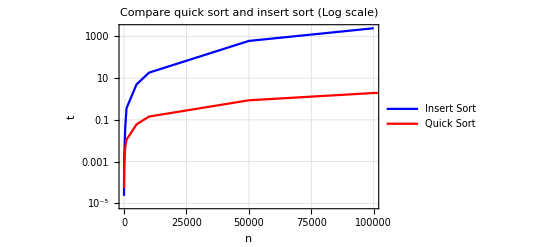

InterpolatingFunction::dmval: Input value {2.04286} lies outside the range of data in the interpolating function. Extrapolation will be used.

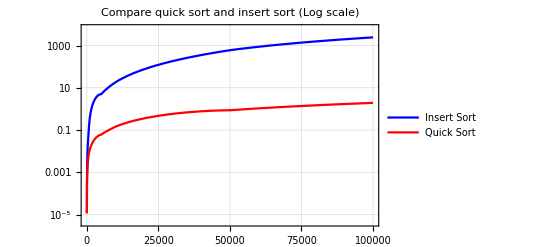

InterpolatingFunction::dmval: Input value {2.04286} lies outside the range of data in the interpolating function. Extrapolation will be used.

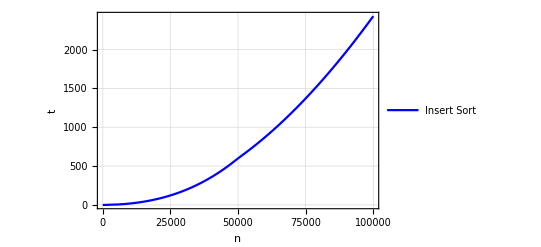

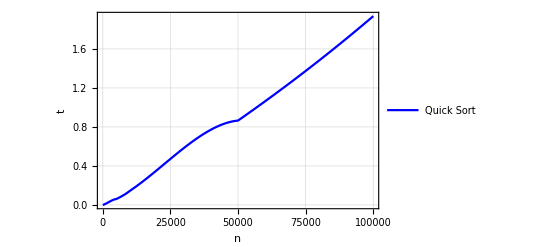

```mathematica
SetDirectory[NotebookDirectory[]];
workingDirectory = CreateDirectory["../shown results"];
SetDirectory[workingDirectory];
file= OpenRead["../logs/log_sort.txt"];
workingDirectory = CreateDirectory["sort"];
SetDirectory[workingDirectory];
filelist= ReadList[file,String];
quickSortResults = filelist[[2;;;;3]];
insertSortResults = filelist[[1;;;;3]];
insertSortResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,insertSortResults][[;;-4]];
quickSortResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,quickSortResults];
insertSortResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,insertSortResults];
quickSortResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,quickSortResults];
Plot1 = Show[ListLogPlot[insertSortResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Insert Sort"},PlotLabel->"Compare quick sort and insert sort (Log scale)", AxesLabel->{"n","t"},PlotTheme->"Detailed"],ListLogPlot[quickSortResults,Joined->True,PlotStyle->Red,PlotLegends->{"Quick Sort"}]]
insertFunc = Interpolation[insertSortResults];
quickFunc = Interpolation[quickSortResults];
Plot2 = LogPlot[{insertFunc[x],quickFunc[x]},{x,0,10^5},PlotStyle->{Blue,Red},PlotLegends->{"Insert Sort","Quick Sort"},PlotLabel->"Compare quick sort and insert sort (Log scale)",PlotTheme->"Detailed"]
Plot3 = Plot[insertFunc[x],{x,0,10^5},PlotStyle->Blue,PlotLegends->{"Insert Sort"},AxesLabel->{"n","t"},PlotTheme->"Detailed"]
Plot4 = Plot[quickFunc[x],{x,0,10^5},PlotStyle->Blue,PlotLegends->{"Quick Sort"},AxesLabel->{"n","t"},PlotTheme->"Detailed"]
```

```mathematica
Export["Comp1.gif",Plot1,ImageSize->2048];
Export["Comp2.gif",Plot2,ImageSize->2048];
Export["Insert.gif",Plot3,ImageSize->2048];
Export["Quick.gif",Plot4,ImageSize->2048];
```

```mathematica
grid = Grid[Transpose[{Join[{"Number"},quickSortResults[[All,1]]],Join[{"Insert sort (sec.)"},insertSortResults[[All,2]],{"-","-","-"}],Join[{"Quick sort (sec.)"},quickSortResults[[All,2]]]}],Frame->All,Alignment->Left,Background->{None,{Yellow}},ItemStyle->Directive[FontSize->20,Bold]]
```

Number | Insert sort (sec.) | Quick sort (sec.)
5 | 0.0000230932 | 0.0000527845
10 | 0.0000392218 | 0.000106302
50 | 0.000408347 | 0.000363627
100 | 0.00173053 | 0.000694263
500 | 0.0441084 | 0.00497384
1000 | 0.358574 | 0.0112999
5000 | 4.95122 | 0.0607704
10000 | 18.1865 | 0.144154
50000 | 600.278 | 0.865415
100000 | 2429.68 | 1.93654
500000 | - | 11.7364
1000000 | - | 24.5791
5000000 | - | 149.887

```mathematica
Export["TableSort.gif",grid,ImageSize->{2048,720}];
Export["TableSort.xls",grid,ImageSize->{2048,720}];
```